```mathematica
Exit[]
```

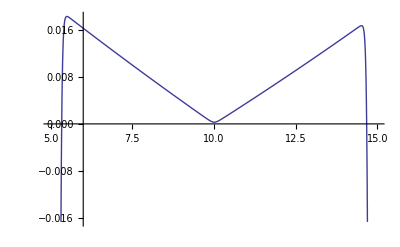

```mathematica
s=0.2;L=0.1;xq=10;r=0.03;k=0.4;t=0.5;xMin=5;xMax=15;
Nx=1000;dx=(xMax-xMin)/Nx;Nt=400;dt=t/Nt;

xs=N[Range[xMin,xMax,dx]];

(*Analytic solution*)
m[x_,t_]:=Exp[-L t]x +(1-Exp[-L t])xq
v[t_]:=s^2/(2 L)(1-Exp[-2 L t])
analytic[x_]:=Exp[-r t-k m[x,t]+1/2 v[t] k^2]

(*numerical solution*)
h[x_]:=Exp[-k x]
step[i_,a_]:=If[a(xs[[i]]-xq)<0,a,0] L/dx(xq-xs[[i]])
G=SparseArray[{{i_,i_}:>1+dt(r+s^2/dx^2+step[i,1]+step[i,-1]), 
{i_,j_}/;Abs[i-j]==1:>- dt(s^2/(2 dx^2) +step[i,If[j==i+1,1,-1]])},
{Nx+1,Nx+1}];

(*relative difference in percent*)
ListLinePlot[Transpose[{xs,100 MatrixPower[G,-Nt].(N[h/@xs])/(analytic/@xs)-100}]]
```